## Kn = 0.1

```mathematica
resultMom = Import["/Users/neerajsarna/sciebo/StaRMAP_ver1p9/SBP_Traditional/generic_1D/result_Inflow/inflow_tend_0.3_points_300_neqn_200.txt","Table"];
resultDVM = Import["/Users/neerajsarna/sciebo/StaRMAP_ver1p9/SBP_Traditional/generic_1D/result_Inflow/DVM_inflow_0.3_points_100_neqn_30.txt","Table"];
```

```mathematica
Clear[interMoments]
```

```mathematica
interMoments = Table[Interpolation[Transpose[{resultMom⟦1,All⟧,resultMom⟦ii,All⟧}]],{ii,2,Length[resultMom]}];
fMom = f0[c]Sum[H[ii-1,c]interMoments⟦ii⟧[x],{ii,1,Length[interMoments]}];
gridV = resultDVM⟦2,All⟧;
gridX = resultDVM⟦1,All⟧;
```

```mathematica
(*we compute the moment distribution function on the discrete velocity grid*)
fPointsMom = Flatten[Table[Table[{ii,jj,fMom/.{x->ii,c->jj}},{jj,gridV}],{ii,gridX}],1];
```

```mathematica
fPointsDVM = Flatten[ Table[Table[{gridX⟦ii⟧,gridV⟦jj⟧,resultDVM⟦jj+2,ii⟧},{jj,1,Length[gridV]}],{ii,1,Length[gridX]}],1];
```

```mathematica
Error =fPointsDVM;
Error⟦All,3⟧=Log10[Abs[fPointsDVM⟦All,3⟧-fPointsMom⟦All,3⟧]];
```

```mathematica
Length[resultDVM⟦1⟧]
```

51

```mathematica
plot = ListPlot3D[fPointsMom,PlotRange->Full,ImageSize->Large,ColorFunction->"Rainbow",AxesLabel->{Style["x",FontSize->14,FontColor->Black],Style["ξ",FontSize->14,FontColor->Black]},TicksStyle->Directive["Label", 14]]
```

-Graphics3D-

```mathematica
Export["/Users/neerajsarna/Dropbox/my_papers/Publications/Convergence_Analysis/results/1D_Inflow/f_mom_Kn0p1.eps",plot]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/Convergence_Analysis/results/1D_Inflow/f_mom_Kn0p1.eps

```mathematica
plot = ListPlot3D[fPointsDVM,PlotRange->Full,ImageSize->Large,ColorFunction->"Rainbow",AxesLabel->{Style["x",FontSize->14,FontColor->Black],Style["ξ",FontSize->14,FontColor->Black]},TicksStyle->Directive["Label", 14]]
```

-Graphics3D-

```mathematica
ListPlot3D[Error,PlotRange->Full,ImageSize->Large,ColorFunction->"Rainbow",AxesLabel->{Style["x",FontSize->14,FontColor->Black],Style["ξ",FontSize->14,FontColor->Black]},TicksStyle->Directive["Label", 14]]
```

-Graphics3D-

## Kn = ∞

```mathematica
Clear[resultMom,fMom]
```

```mathematica
Exactf[c_]:=Piecewise[{{f0[c]H[2,c],c≤0},{-f0[c]H[2,c],c>0}}];
```

```mathematica
Mvalues =Sort[Flatten[ {Range[4,24,4],Range[5,25,4 ]}]];
Do[resultMom[ii]=Import[StringJoin["/Users/neerajsarna/sciebo/StaRMAP_ver1p9/SBP_Traditional/generic_1D/result_Inflow_KnInf_Steady/inflow_tend_0.3_points_300_neqn_",ToString[ii],".txt"],"Table"];
fMom[ii] = f0[c]Sum[H[jj-2,c]resultMom[ii]⟦jj,1⟧,{jj,2,Length[resultMom[ii]]}];
,{ii,Mvalues}];
```

```mathematica
errorvalues = Quiet[Table[Sqrt[NIntegrate[(Exactf[c]-fMom[ii])^2(f0[c])^-1,{c,-10,10},AccuracyGoal->Infinity,WorkingPrecision->32,PrecisionGoal->8,MaxRecursion->20]],{ii,Mvalues}]];
```

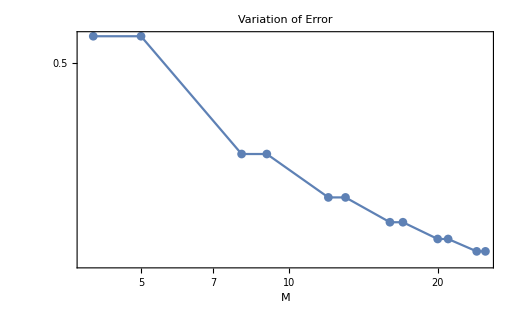

```mathematica
ListLogLogPlot[Transpose[{Mvalues,errorvalues}],GridLines->Automatic,Joined->True,PlotMarkers->Automatic,Frame->True,FrameTicksStyle->14,FrameLabel->{{None,None},{Style["M",FontSize->14,FontColor->Black],None}},RotateLabel->False,PlotLabel->Style["Variation of Error",FontSize->14,FontColor->Black]]
```

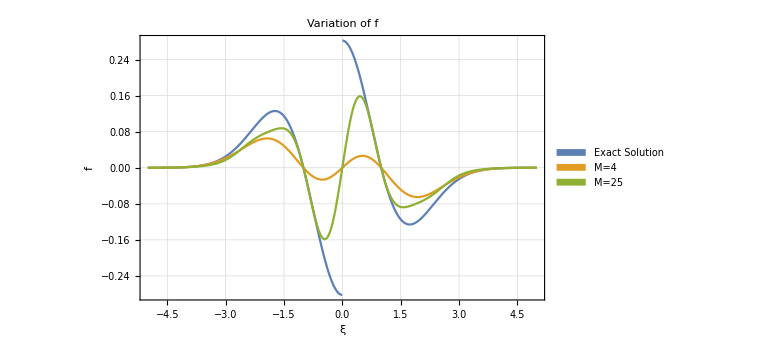

```mathematica
Plot[{Exactf[c],fMom[4],fMom[24]},{c,-5,5},PlotRange->Full,Frame->True,FrameTicksStyle->14,FrameLabel->{{Style["f",FontSize->14,FontColor->Black],None},{Style["ξ",FontSize->14,FontColor->Black],None}},RotateLabel->False,PlotLabel->Style["Variation of f",FontSize->14,FontColor->Black],GridLines->Automatic,PlotLegends->Placed[SwatchLegend[{"Exact Solution","M=4","M=25"}],{0.8,0.8}],ImageSize->Large]
```

## Heat Conduction

### Heat Conduction

```mathematica
exactHCKn0p1 = Import["/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files/refs/Archive/BGKSimpleHeat/Result_BGKreduced_tau0p1_nst600_Nc300_cMax5p0.dat"];

(*200, 020 and 002 are the variable number 3 4 5 + 1 for the space points*)
exactHCMomKn0p1=Transpose[Import["/Users/neerajsarna/sciebo/StaRMAP_ver1p9/SBP_Traditional/generic_1D/result_HC2D/hc_tend_1_points_300_neqn_55.txt","Table"]];

(*fix for the wall temperature*)
(*exactHCKn0p1⟦All,4⟧+=1;
exactHCKn0p3⟦All,4⟧+=1;
exactHCKn0p5⟦All,4⟧+=1;*)

θExactHCKn0p1=Interpolation[exactHCKn0p1⟦All,{1,4}⟧];
σExactHCKn0p1 = Interpolation[exactHCKn0p1⟦All,{1,6}⟧];
qExacHCtKn0p1 = Interpolation[exactHCKn0p1⟦All,{1,7}⟧];

w200=Interpolation[exactHCMomKn0p1⟦All,{1,4}⟧];
w020 = Interpolation[exactHCMomKn0p1⟦All,{1,5}⟧];
w002 = Interpolation[exactHCMomKn0p1⟦All,{1,6}⟧];
```

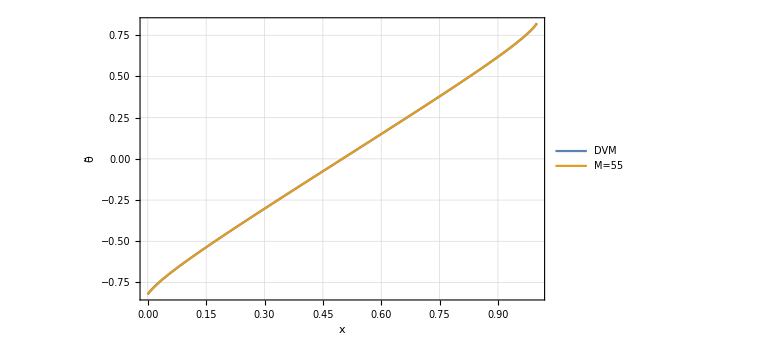

```mathematica
Plot[{(-θExactHCKn0p1[t]/.{t->(x-0.5)}),(√2)/3(w200[x]+w020[x]+w002[x])},{x,0,1},PlotRange->Full,GridLines->Automatic,Frame->True,FrameTicksStyle->18,FrameLabel->{{Style["θ̃",FontSize->18],None},{Style["x",FontSize->18],None}},RotateLabel->False,PlotLegends->Placed[{"DVM","M=55"},{0.7,0.5}],ImageSize->Large]
```

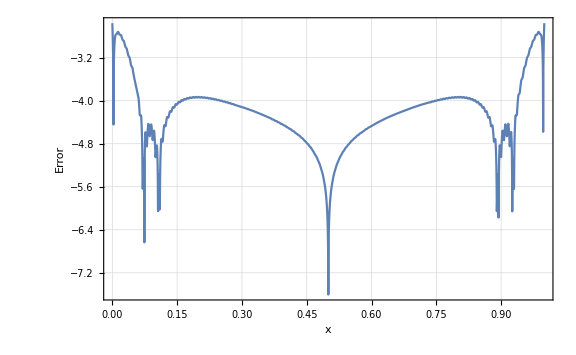

```mathematica
Plot[Log10[Abs[(-θExactHCKn0p1[t]/.{t->(x-0.5)})-(√2)/3(w200[x]+w020[x]+w002[x])]],{x,0,1},PlotRange->Full,GridLines->Automatic,Frame->True,FrameTicksStyle->18,FrameLabel->{{Style["Error",FontSize->18],None},{Style["x",FontSize->18],None}},ImageSize->Large]
```

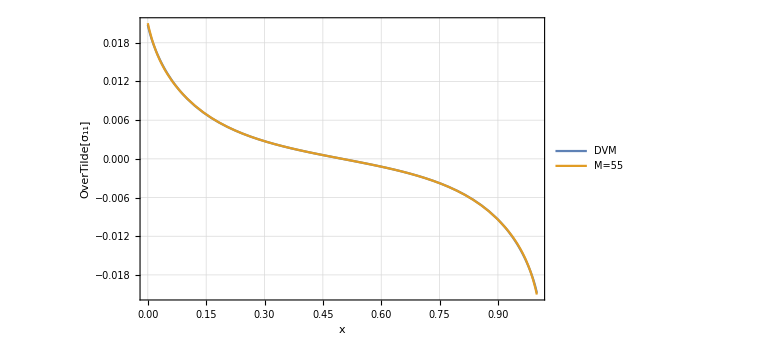

```mathematica
Plot[{(-σExactHCKn0p1[t]/.{t->(x-0.5)}),(√2)/3(2w200[x]-w020[x]-w002[x])},{x,0,1},PlotRange->Full,GridLines->Automatic,Frame->True,FrameTicksStyle->18,FrameLabel->{{Style["OverTilde[σ_11]",FontSize->18],None},{Style["x",FontSize->18],None}},RotateLabel->False,PlotLegends->Placed[{"DVM","M=55"},{0.7,0.6}],ImageSize->Large]
```

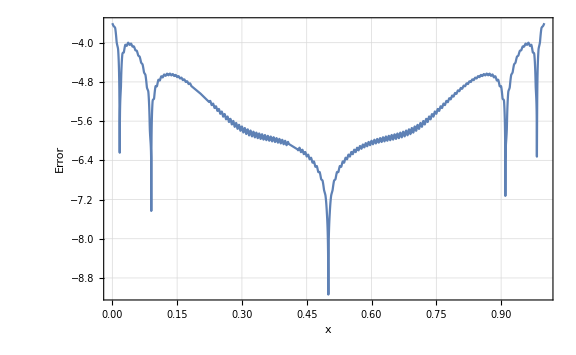

```mathematica
Plot[Log10[Abs[(-σExactHCKn0p1[t]/.{t->(x-0.5)})-(√2)/3(2w200[x]-w020[x]-w002[x])]],{x,0,1},PlotRange->Full,GridLines->Automatic,Frame->True,FrameTicksStyle->18,FrameLabel->{{Style["Error",FontSize->18],None},{Style["x",FontSize->18],None}},ImageSize->Large]
```

```mathematica
Total[Table[Length[Select[IDXFull[ii],(#⟦2⟧==0&&#⟦3⟧==2)||(#⟦2⟧==2&&#⟦3⟧==0)&]],{ii,0,55}]]
```

108